# NG^23 T_10.Свёртка. Фильтрация изображений

Ковалевская Варвара,
06-апр-2023

## Section. Вычисление производных

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory";
Get["NG23T10Problem.mx","NG23T10"];
```

```mathematica
F1=NG23T10`kmF1
```

Piecewise[{{1-#1, #1<1}, {#1-1, #1<2}, {1, #1<3}, {1/5 (28 #1^2-201 #1+361), #1<4}, {Sin[π (#1-3)^1.5]+1, True}}]&

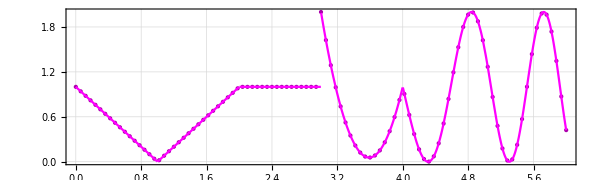

```mathematica
Show[ListPlot[X1=Array[F1,101 ,{0.,6}],DataRange->{0,6},AspectRatio->0.3,ImageSize->600,Frame->True,GridLines->Automatic,PlotStyle->Directive[PointSize@Large,Darker@Magenta]],
Plot[F1@t,{t,0,6},PlotStyle->Magenta]]
```

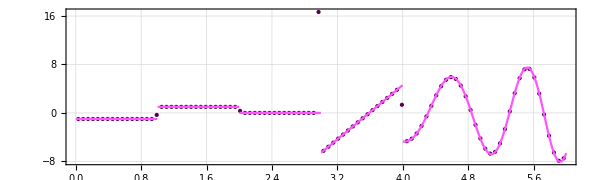

```mathematica
Show[ListPlot[
X11=ListConvolve[{1,-1}/0.06,X1],DataRange->{0+0.03,6-0.03},AspectRatio->0.3,ImageSize->600,Frame->True,GridLines->Automatic,PlotStyle->Directive[PointSize@Large,Darker@Purple]],
Plot[F1'@t,{t,0,6},PlotStyle->Lighter@Magenta],PlotRange->All]
```

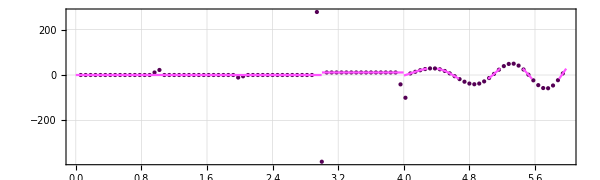

```mathematica
Show[ListPlot[
X12=ListConvolve[{1,-2,1}/0.06^2,X1],DataRange->{0+0.06,6-0.06},AspectRatio->0.3,ImageSize->600,Frame->True,GridLines->Automatic,PlotStyle->Directive[PointSize@Large,Darker@Purple]],
Plot[F1''@t,{t,0,6},PlotStyle->Lighter@Magenta],PlotRange->All]
```

## Section. Сглаживание фильтрами Гаусса

```mathematica
F2=NG23T10`kmF2
```

2 Sin[√#1]+Sin[3 #1^0.7]&

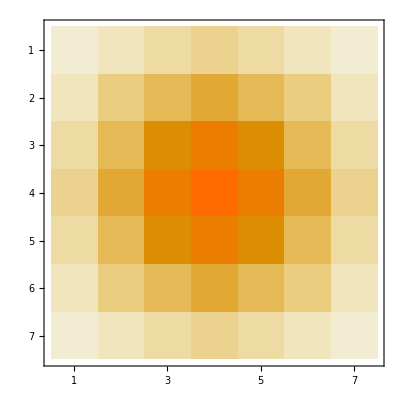
{(0.00121055 | 0.00354909 | 0.00752005 | 0.0102336 | 0.00752005 | 0.00354909 | 0.00121055
0.00354909 | 0.0104052 | 0.0220473 | 0.0300028 | 0.0220473 | 0.0104052 | 0.00354909
0.00752005 | 0.0220473 | 0.0467152 | 0.0635719 | 0.0467152 | 0.0220473 | 0.00752005
0.0102336 | 0.0300028 | 0.0635719 | 0.0865112 | 0.0635719 | 0.0300028 | 0.0102336
0.00752005 | 0.0220473 | 0.0467152 | 0.0635719 | 0.0467152 | 0.0220473 | 0.00752005
0.00354909 | 0.0104052 | 0.0220473 | 0.0300028 | 0.0220473 | 0.0104052 | 0.00354909
0.00121055 | 0.00354909 | 0.00752005 | 0.0102336 | 0.00752005 | 0.00354909 | 0.00121055),-Graphics-}

```mathematica
Through@{MatrixForm,MatrixPlot}@GaussianMatrix[3]
```

```mathematica
GaussianMatrix[{{5}}]
```

{0.0216149,0.0439554,0.0778778,0.118718,0.153857,0.167953,0.153857,0.118718,0.0778778,0.0439554,0.0216149}

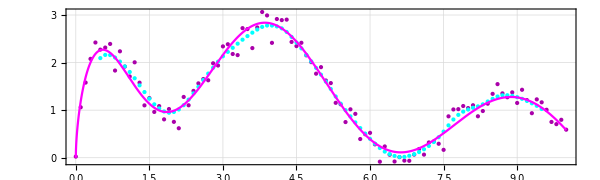

```mathematica
Show[ListPlot[X2=Array[F2,101 ,{0.,10}]+RandomVariate[NormalDistribution[0,0.2],101],DataRange->{0,10},AspectRatio->0.3,ImageSize->600,Frame->True,GridLines->Automatic,PlotStyle->Directive[PointSize@Large,Darker@Magenta]],
ListPlot[X2G=ListConvolve[GaussianMatrix@{{5}},X2],DataRange->{0+0.5,10-0.5},PlotStyle->Directive[PointSize@Large,Cyan]],
Plot[F2@t,{t,0,10},PlotStyle->Magenta]]
```

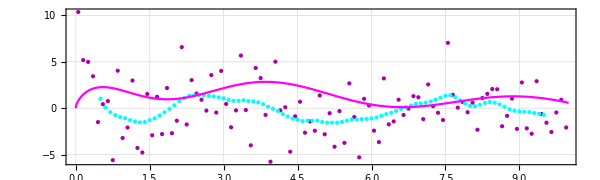

```mathematica
Show[ListPlot[X21=ListConvolve[{1,-1}/0.1,X2],DataRange->{0+0.05,10-0.05},AspectRatio->0.3,ImageSize->600,Frame->True,GridLines->Automatic,PlotStyle->Directive[PointSize@Large,Darker@Magenta]],
ListPlot[ListConvolve[GaussianMatrix[{{5}},1]/0.1,X2],DataRange->{0+0.5,10-0.5},PlotStyle->Directive[PointSize@Large,Cyan]],
Plot[F2@t,{t,0,10},PlotStyle->Magenta]]
```

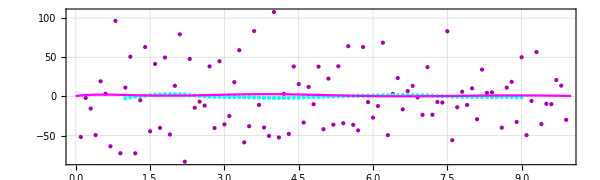

```mathematica
Show[ListPlot[X22=ListConvolve[{1,-2,1}/0.1^2,X2],DataRange->{0+0.1,10-0.1},AspectRatio->0.3,ImageSize->600,Frame->True,GridLines->Automatic,PlotStyle->Directive[PointSize@Large,Darker@Magenta]],
ListPlot[ListConvolve[GaussianMatrix[{{10}},2]/0.1^2,X2],DataRange->{0+1,10-1},PlotStyle->Directive[PointSize@Large,Cyan]],
Plot[F2@t,{t,0,10},PlotStyle->Magenta]]
```

## Section. Свёртка изображений

```mathematica
Through@{MinMax,Dimensions}[Pic=NG23T10`kmPic]
```

{{0.,1.},{1024,1024}}

```mathematica
Image[Pic,ImageSize->200]
```

```mathematica
RandomReal[10 {-1,1},{9,9}];
Image[%]
ImageAdjust@%
```

-Graphics-

-Graphics-

```mathematica
RandomReal[10 {-1,1},{9,9}];
ImageAdjust@Image[%]
Image[Rescale@%%]
```

-Graphics-

-Graphics-

```mathematica
ClearAll[kmShow];
kmShow[X_,opts___]:=Image[Rescale@X,opts,ImageSize->200]
```

```mathematica
kmShow[Pic,ImageSize->50]
```

```mathematica
ker1=RandomReal[{-1,1},{5,5}]
```

{{-0.552532,-0.563281,-0.40022,0.457708,0.45041},{0.19061,-0.74312,0.763761,-0.291668,-0.36271},{0.0668052,0.204001,-0.533738,-0.625335,-0.813889},{0.528798,0.677505,0.508895,-0.35631,-0.344915},{0.130315,0.127195,0.0986558,-0.429382,0.541335}}

```mathematica
Total[ker1,2]
```

-0.0415244

```mathematica
ker1=#/Total[#,2]&@RandomReal[{-1,1},{5,5}];
RightArrow[
kmShow@Pic,
MatrixPlot[ker1,ImageSize->100,ColorFunction->"GreenPinkTones"],
kmShow@ListConvolve[ker1,Pic]
]
```

```mathematica
ker2=#/Total[#,2]&@ConstantArray[1.,{50,50}];
RightArrow[
kmShow@Pic,
MatrixPlot[ker2,ImageSize->100,ColorFunction->"GreenPinkTones"],
kmShow@ListConvolve[ker2,Pic]
]
```

```mathematica
ker3
```

{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{0.,0.,0.,0.,0.},{-1.,-1.,-1.,-1.,-1.},{-1.,-1.,-1.,-1.,-1.}}

```mathematica
ker3=ConstantArray[0.,{5,5}];
ker3[[-2;;,All]]=-(ker3[[;;2,All]]=1.)
RightArrow[
kmShow@Pic,
MatrixPlot[ker3,ImageSize->100,ColorFunction->"GreenPinkTones"],
kmShow@ListConvolve[ker3,Pic]
]
```

-1.

## Section. Фильтрация изображений

```mathematica
GaussianMatrix[5];
RightArrow[
kmShow@Pic,
MatrixPlot[%,ImageSize->100,ColorFunction->"GreenPinkTones"],
kmShow@ListConvolve[%,Pic]
]
```

```mathematica
GaussianMatrix[5,{1,0}];
RightArrow[
kmShow@Pic,
MatrixPlot[%,ImageSize->100,ColorFunction->"GreenPinkTones"],
kmShow@ListConvolve[%,Pic]
]
```

```mathematica
GaussianMatrix[5,{0,1}];
RightArrow[
kmShow@Pic,
MatrixPlot[%,ImageSize->100,ColorFunction->"GreenPinkTones"],
kmShow@ListConvolve[%,Pic]
]
```

```mathematica
GaussianMatrix[5,{{2,0},{0,2}}];
RightArrow[
kmShow@Pic,
MatrixPlot[%,ImageSize->100,ColorFunction->"GreenPinkTones"],
kmShow@ListConvolve[%,Pic]
]
```

## Section. Рецепторные поля свёрточного нейрона

## Section. Эффекторные поля свёрточного нейрона